## Initial setup

```mathematica
Remove["Global`*"]
```

```mathematica
e = 0.000000001;
maxDepth = 3;
```

## Point sampling (current example)

```mathematica
npoints = 10;
sp = SpherePoints[npoints];
```

```mathematica
sn = sp;
```

```mathematica
plt1 = Show[
Table[Graphics3D[Arrow[{sp[[i]], sp[[i]]+sn[[i]]}]],{i,npoints}],
ListPointPlot3D[sp, AspectRatio->1]
]
```

-Graphics3D-

## Octree spatial partition

```mathematica
initialWidth = Max[(Max@sp[[All,#]]&/@Range[3])-(Min@sp[[All,#]]&/@Range[3])] + 2.00 * e
```

1.78885

```mathematica
initialCenter = ((Max@sp[[All,#]]&/@Range[3])+(Min@sp[[All,#]]&/@Range[3]))/2.00
```

{0.,0.,0.}

```mathematica
{xmin, ymin, zmin} = initialCenter - initialWidth * 0.65;
{xmax, ymax, zmax} = initialCenter + initialWidth * 0.65;
```

```mathematica
(* { {{center}, width}, {idx1, idx2, idx3, ...} } *)
octree = {{{initialCenter, initialWidth},Table[i, {i,Length[sp]}]}};
```

```mathematica
SubdivideNode[node_, pts_]:=Module[{n, points, idx, center, width, child1, child2, child3, child4, child5, child6, child7, child8, result},
n=node;
points=pts;
idx = n[[2]];
center = n[[1]][[1]];
width = n[[1]][[2]];
(* Subdivide only if the node has more than 1 points *)
If[Length[idx]>1,
(* True: Subdivide *)
child1 = {};
child2 = {};
child3 = {};
child4 = {};
child5 = {};
child6 = {};
child7 = {};
child8 = {};
Do[ (* for each point in the node *)
If[points[[idx[[i]]]][[1]] ≤ center[[1]] && points[[idx[[i]]]][[2]] ≤ center[[2]] && points[[idx[[i]]]][[3]] ≤ center[[3]],child1 = Append[child1, idx[[i]]]];
If[points[[idx[[i]]]][[1]] > center[[1]] && points[[idx[[i]]]][[2]] ≤ center[[2]] && points[[idx[[i]]]][[3]] ≤ center[[3]],child2 = Append[child2, idx[[i]]]];
If[points[[idx[[i]]]][[1]] ≤ center[[1]] && points[[idx[[i]]]][[2]] > center[[2]] && points[[idx[[i]]]][[3]] ≤ center[[3]],child3 = Append[child3, idx[[i]]]];
If[points[[idx[[i]]]][[1]] > center[[1]] && points[[idx[[i]]]][[2]] > center[[2]] && points[[idx[[i]]]][[3]] ≤ center[[3]],child4 = Append[child4, idx[[i]]]];
If[points[[idx[[i]]]][[1]] ≤ center[[1]] && points[[idx[[i]]]][[2]] ≤ center[[2]] && points[[idx[[i]]]][[3]] > center[[3]],child5 = Append[child5, idx[[i]]]];
If[points[[idx[[i]]]][[1]] > center[[1]] && points[[idx[[i]]]][[2]] ≤ center[[2]] && points[[idx[[i]]]][[3]] > center[[3]],child6 = Append[child6, idx[[i]]]];
If[points[[idx[[i]]]][[1]] ≤ center[[1]] && points[[idx[[i]]]][[2]] > center[[2]] && points[[idx[[i]]]][[3]] > center[[3]],child7 = Append[child7, idx[[i]]]];
If[points[[idx[[i]]]][[1]] > center[[1]] && points[[idx[[i]]]][[2]] > center[[2]] && points[[idx[[i]]]][[3]] > center[[3]],child8 = Append[child8, idx[[i]]]]
,{i,Length[idx]}];
(* Construct what to return *)
result = {};
If[Length[child1]>0, result=Append[result,{{center+{-width/4.0, -width/4.0, -width/4.0}, width/2.0},child1}]];
If[Length[child2]>0, result=Append[result,{{center+{+width/4.0, -width/4.0, -width/4.0}, width/2.0},child2}]];
If[Length[child3]>0, result=Append[result,{{center+{-width/4.0, +width/4.0, -width/4.0}, width/2.0},child3}]];
If[Length[child4]>0, result=Append[result,{{center+{+width/4.0, +width/4.0, -width/4.0}, width/2.0},child4}]];
If[Length[child5]>0, result=Append[result,{{center+{-width/4.0, -width/4.0, +width/4.0}, width/2.0},child5}]];
If[Length[child6]>0, result=Append[result,{{center+{+width/4.0, -width/4.0, +width/4.0}, width/2.0},child6}]];
If[Length[child7]>0, result=Append[result,{{center+{-width/4.0, +width/4.0, +width/4.0}, width/2.0},child7}]];
If[Length[child8]>0, result=Append[result,{{center+{+width/4.0, +width/4.0, +width/4.0}, width/2.0},child8}]];
n = result;,
(* else *)
n = {n};
]; (* end if *)
n] (* end function *)
```

```mathematica
SubdivideOctree[oct_, pts_]:=Module[{tr, points, output, result},
tr=oct;
points=pts;
output = {};
Do[
result =SubdivideNode[tr[[i]],points];
 Do[output = Append[output,result[[j]]],{j,Length[result]}],
{i, Length[tr]}
];
output
]
```

```mathematica
octree
```

{{{{0.,0.,0.},1.78885},{1,2,3,4,5,6,7,8,9,10}}}

```mathematica
Do[octree = SubdivideOctree[octree, sp], {i,maxDepth}]
```

```mathematica
nleaves = Length[octree]
```

10

## System

```mathematica
F[q_]:=(2π)^(-3/2)*Exp[-1/2 qᵀ.q]
```

```mathematica
Fo[q_,c_,w_]:=F[1/w*(q-c)]
```

```mathematica
(* Gradient field *)
```

```mathematica
V[q_]:=Sum[
Sum[
Fo[
q,
 octree[[i]][[1]][[1]], (* leaf i center *)
octree[[i]][[1]][[2]] (* leaf i width *)
]
 * sn[[  
octree[[i]][[2]][[j]]  (* j-th index of contents of leaf i *)
 ]],
{j, Length[ octree[[i]][[2]]]}], (* iterate over the contents of leaf i *)
{i,nleaves}] (* iterate over leaves *)
```

```mathematica
Show[
VectorPlot3D[V[{x,y,z}],{x,xmin,xmax},{y,ymin,ymax},{z,zmin,zmax}, VectorScaling-> Automatic],
plt1]
```

-Graphics3D-

```mathematica
divV[{x_,y_,z_}]:=(V[{x+e, y, z}][[1]]-V[{x, y, z}][[1]])/e+(V[{x, y+e, z}][[2]]-V[{x, y, z}][[2]])/e+(V[{x, y, z+e}][[3]]-V[{x, y, z}][[3]])/e
```

```mathematica
dFox[{x_,y_,z_},{cx_,cy_,cz_},w_] = D[Fo[{x,y,z},{cx,cy,cz},w],x]
```

-(ⅇ^(1/2 (-(-cx+x)^2/w^2-(-cy+y)^2/w^2-(-cz+z)^2/w^2)) (-cx+x))/(2 √2 π^(3/2) w^2)

```mathematica
dFoy[{x_,y_,z_},{cx_,cy_,cz_},w_] = D[Fo[{x,y,z},{cx,cy,cz},w],y]
```

-(ⅇ^(1/2 (-(-cx+x)^2/w^2-(-cy+y)^2/w^2-(-cz+z)^2/w^2)) (-cy+y))/(2 √2 π^(3/2) w^2)

```mathematica
dFoz[{x_,y_,z_},{cx_,cy_,cz_},w_] = D[Fo[{x,y,z},{cx,cy,cz},w],z]
```

-(ⅇ^(1/2 (-(-cx+x)^2/w^2-(-cy+y)^2/w^2-(-cz+z)^2/w^2)) (-cz+z))/(2 √2 π^(3/2) w^2)

```mathematica
(* symbolic divergance of vector field *)
divV2[{x_,y_,z_}]=Sum[
Sum[
{dFox[
{x,y,z},
 octree[[i]][[1]][[1]], (* leaf i center *)
octree[[i]][[1]][[2]] (* leaf i width *)
] ,
dFoy[
{x,y,z},
 octree[[i]][[1]][[1]], (* leaf i center *)
octree[[i]][[1]][[2]] (* leaf i width *)
],
dFoz[
{x,y,z},
 octree[[i]][[1]][[1]], (* leaf i center *)
octree[[i]][[1]][[2]] (* leaf i width *)
]}ᵀ
 . sn[[  
octree[[i]][[2]][[j]]  (* j-th index of contents of leaf i *)
 ]] 
,
{j, Length[ octree[[i]][[2]]]}], (* iterate over the contents of leaf i *)
{i,nleaves}];(* iterate over leaves *)
```

```mathematica
divV[{1,0,1}]
```

0.0235497

```mathematica
divV2[{1,0,1}] (* same results: ok *)
```

0.0235497

```mathematica
NIntegrate[divV2[{x,y,z}]*Fo[{x,y,z}, octree[[1]][[1]][[1]],octree[[1]][[1]][[2]]], {x,xmin,xmax},{y,ymin,ymax},{z,zmin,zmax}, Method-> "GlobalAdaptive", AccuracyGoal->50]
```

0.0138252

```mathematica
(* Fxo1o2[{c1x_,c1y_,c1z_},{c2x_,c2y_,c2z_},w1_,w2_]=Integrate[dFox[{x,y,z},{c1x,c1y,c1z},w1]*Fo[{x,y,z},{c2x, c2y, c2z}, w2],
{x,-Infinity,Infinity},
 {y,-Infinity,Infinity},
{z,-Infinity,Infinity},
Assumptions-> {c1x∈Reals,c1y∈Reals,c1z∈Reals,c2x∈Reals,c2y∈Reals,c2z∈Reals,w1∈Reals, w2∈Reals, w1>0, w2>0}] *)
```

```mathematica
(* This is the result we get, it takes too long to get it: *)
Fxo1o2[{c1x_,c1y_,c1z_},{c2x_,c2y_,c2z_},w1_,w2_]=((c1x-c2x) ⅇ^(-(c1x^2+c1y^2+c1z^2-2 c1x c2x+c2x^2-2 c1y c2y+c2y^2-2 c1z c2z+c2z^2)/(2 (w1^2+w2^2))) w1^3 w2^3)/(2 √2 π^(3/2) (w1^2+w2^2)^(5/2));
```

```mathematica
(* Fyo1o2[{c1x_,c1y_,c1z_},{c2x_,c2y_,c2z_},w1_,w2_]=Once[
Integrate[dFoy[{x,y,z},{c1x,c1y,c1z},w1]*Fo[{x,y,z},{c2x, c2y, c2z}, w2],
{x,-Infinity,Infinity},
 {y,-Infinity,Infinity},
{z,-Infinity,Infinity},
Assumptions-> {c1x∈Reals,c1y∈Reals,c1z∈Reals,c2x∈Reals,c2y∈Reals,c2z∈Reals,w1∈Reals, w2∈Reals, w1>0, w2>0}],
"Fyo1o2"] *)
```

```mathematica
Fyo1o2[{c1x_,c1y_,c1z_},{c2x_,c2y_,c2z_},w1_,w2_] = ((c1y-c2y) ⅇ^(-(c1x^2+c1y^2+c1z^2-2 c1x c2x+c2x^2-2 c1y c2y+c2y^2-2 c1z c2z+c2z^2)/(2 (w1^2+w2^2))) w1^3 w2^3)/(2 √2 π^(3/2) (w1^2+w2^2)^(5/2));
```

```mathematica
(* Fzo1o2[{c1x_,c1y_,c1z_},{c2x_,c2y_,c2z_},w1_,w2_]=Once[
Integrate[dFoz[{x,y,z},{c1x,c1y,c1z},w1]*Fo[{x,y,z},{c2x, c2y, c2z}, w2],
{x,-Infinity,Infinity},
 {y,-Infinity,Infinity},
{z,-Infinity,Infinity},
Assumptions-> {c1x∈Reals,c1y∈Reals,c1z∈Reals,c2x∈Reals,c2y∈Reals,c2z∈Reals,w1∈Reals, w2∈Reals, w1>0, w2>0}],
"Fzo1o2"] *)
```

```mathematica
Fzo1o2[{c1x_,c1y_,c1z_},{c2x_,c2y_,c2z_},w1_,w2_] =((c1z-c2z) ⅇ^(-(c1x^2+c1y^2+c1z^2-2 c1x c2x+c2x^2-2 c1y c2y+c2y^2-2 c1z c2z+c2z^2)/(2 (w1^2+w2^2))) w1^3 w2^3)/(2 √2 π^(3/2) (w1^2+w2^2)^(5/2));
```

```mathematica
v = Table[
NIntegrate[divV[{x,y,z}]*Fo[{x,y,z}, octree[[i]][[1]][[1]],octree[[i]][[1]][[2]]], {x,xmin,xmax},{y,ymin,ymax},{z,zmin,zmax}, Method-> "GlobalAdaptive", AccuracyGoal->50],{i,nleaves}]
```

{0.0138252,0.0120902,0.0379782,0.034036,0.0339519,0.0379782,0.0138252,0.0120902,0.0339519,0.034036}

```mathematica
vv = Table[
Sum[ (* for every other leaf j *)
(* i: the leaf that corresponds to the element of v we are calculating *)
(* j: any other leaf, i included *)
(* octree[[j]][[2]][[k]]: the k-th index of the contents of leaf node j *)
(* sn[[  octree[[j]][[2]][[k]]  ]]: the normal vector of the corresponding sample point *) 
(* octree[[i]][[1]][[1]]: the center of leaf node i *)
(* octree[[j]][[1]][[1]]: the center of leaf node j *)
(* octree[[i]][[1]][[2]]: the width of leaf node i *)
(* octree[[j]][[1]][[2]]: the width of leaf node j *)
Sum[ (* for every sample in leaf j *)
{Fxo1o2[octree[[j]][[1]][[1]],octree[[i]][[1]][[1]],octree[[j]][[1]][[2]],octree[[i]][[1]][[2]]],
Fyo1o2[octree[[j]][[1]][[1]],octree[[i]][[1]][[1]],octree[[j]][[1]][[2]],octree[[i]][[1]][[2]]],
Fzo1o2[octree[[j]][[1]][[1]],octree[[i]][[1]][[1]],octree[[j]][[1]][[2]],octree[[i]][[1]][[2]]]}ᵀ.sn[[  octree[[j]][[2]][[  k  ]]  ]]
,
{k,Length[octree[[j]][[2]]]}]
,
{j, nleaves}]
,
{i,nleaves}]
```

{0.0138897,0.0120921,0.0360342,0.0299686,0.0288678,0.0360342,0.0138897,0.0120921,0.0288678,0.0299686}

```mathematica
octree
```

{{{{-0.223607,-0.67082,-0.223607},0.447214},{5}},{{{-0.67082,-0.223607,-0.223607},0.447214},{1}},{{{0.447214,-0.447214,-0.447214},0.894427},{9}},{{{-0.447214,0.447214,-0.447214},0.894427},{6}},{{{0.447214,0.447214,-0.447214},0.894427},{10}},{{{-0.447214,-0.447214,0.447214},0.894427},{3}},{{{0.223607,-0.67082,0.223607},0.447214},{7}},{{{0.67082,-0.223607,0.223607},0.447214},{2}},{{{-0.447214,0.447214,0.447214},0.894427},{4}},{{{0.447214,0.447214,0.447214},0.894427},{8}}}

```mathematica
(* Fxxo1o2 = Integrate[D[Fo[{x,y,z},{c1x,c1y,c1z},w1],x,x] * Fo[{x,y,z},{c2x,c2y,c2z},w2],
{x,-Infinity,Infinity},
{y,-Infinity,Infinity},
{z,-Infinity,Infinity},
Assumptions-> {c1x∈Reals,c1y∈Reals,c1z∈Reals,c2x∈Reals,c2y∈Reals,c2z∈Reals,w1∈Reals, w2∈Reals, w1>0, w2>0}] *)
```

```mathematica
Fxxo1o2[{c1x_,c1y_,c1z_},{c2x_,c2y_,c2z_},w1_,w2_] = -(ⅇ^(-(c1x^2+c1y^2+c1z^2-2 c1x c2x+c2x^2-2 c1y c2y+c2y^2-2 c1z c2z+c2z^2)/(2 (w1^2+w2^2))) w1^3 w2^3 (-c1x^2+2 c1x c2x-c2x^2+w1^2+w2^2))/(2 √2 π^(3/2) (w1^2+w2^2)^(7/2));
```

```mathematica
(* Integrate[D[Fo[{x,y,z},{c1x,c1y,c1z},w1],y,y] * Fo[{x,y,z},{c2x,c2y,c2z},w2],
{x,-Infinity,Infinity},
{y,-Infinity,Infinity},
{z,-Infinity,Infinity},
Assumptions-> {c1x∈Reals,c1y∈Reals,c1z∈Reals,c2x∈Reals,c2y∈Reals,c2z∈Reals,w1∈Reals, w2∈Reals, w1>0, w2>0}] *)
```

```mathematica
Fyyo1o2[{c1x_,c1y_,c1z_},{c2x_,c2y_,c2z_},w1_,w2_] = -(ⅇ^(-(c1x^2+c1y^2+c1z^2-2 c1x c2x+c2x^2-2 c1y c2y+c2y^2-2 c1z c2z+c2z^2)/(2 (w1^2+w2^2))) w1^3 w2^3 (-c1y^2+2 c1y c2y-c2y^2+w1^2+w2^2))/(2 √2 π^(3/2) (w1^2+w2^2)^(7/2));
```

```mathematica
(* Integrate[D[Fo[{x,y,z},{c1x,c1y,c1z},w1],z,z] * Fo[{x,y,z},{c2x,c2y,c2z},w2],
{x,-Infinity,Infinity},
{y,-Infinity,Infinity},
{z,-Infinity,Infinity},
Assumptions-> {c1x∈Reals,c1y∈Reals,c1z∈Reals,c2x∈Reals,c2y∈Reals,c2z∈Reals,w1∈Reals, w2∈Reals, w1>0, w2>0}] *)
```

```mathematica
Fzzo1o2[{c1x_,c1y_,c1z_},{c2x_,c2y_,c2z_},w1_,w2_] = (ⅇ^(-(c1x^2+c1y^2+c1z^2-2 c1x c2x+c2x^2-2 c1y c2y+c2y^2-2 c1z c2z+c2z^2)/(2 (w1^2+w2^2))) w1^3 w2^3 (c1z^2-2 c1z c2z+c2z^2-w1^2-w2^2))/(2 √2 π^(3/2) (w1^2+w2^2)^(7/2));
```

```mathematica
LL=Table[
Total[{
Fxxo1o2[octree[[i]][[1]][[1]],octree[[j]][[1]][[1]],octree[[i]][[1]][[2]],octree[[j]][[1]][[2]]],
Fyyo1o2[octree[[i]][[1]][[1]],octree[[j]][[1]][[1]],octree[[i]][[1]][[2]],octree[[j]][[1]][[2]]],
Fzzo1o2[octree[[i]][[1]][[1]],octree[[j]][[1]][[1]],octree[[i]][[1]][[2]],octree[[j]][[1]][[2]]]
}]
,
{i,nleaves},{j,nleaves}]
```

{{-0.0150588,-0.0060891,-0.00756215,-0.00341386,-0.00211745,-0.00756215,-0.0060891,-4.33681×10^-19,-0.00211745,-0.00117886},{-0.0060891,-0.0150588,-0.00341386,-0.00756215,-0.00211745,-0.00756215,-2.1684×10^-19,0.00082407,-0.00518053,-0.00117886},{-0.00756215,-0.00341386,-0.0301177,-0.0121782,-0.0195464,-0.0121782,-0.00756215,-0.00756215,-0.00711329,-0.0121782},{-0.00341386,-0.00756215,-0.0121782,-0.0301177,-0.0195464,-0.0121782,-0.00117886,-0.00117886,-0.0195464,-0.0121782},{-0.00211745,-0.00211745,-0.0195464,-0.0195464,-0.0301177,-0.00711329,-0.00211745,-0.00518053,-0.0121782,-0.0195464},{-0.00756215,-0.00756215,-0.0121782,-0.0121782,-0.00711329,-0.0301177,-0.00756215,-0.00341386,-0.0195464,-0.0121782},{-0.0060891,-4.33681×10^-19,-0.00756215,-0.00117886,-0.00211745,-0.00756215,-0.0150588,-0.0060891,-0.00211745,-0.00341386},{-2.1684×10^-19,0.00082407,-0.00756215,-0.00117886,-0.00518053,-0.00341386,-0.0060891,-0.0150588,-0.00211745,-0.00756215},{-0.00211745,-0.00518053,-0.00711329,-0.0195464,-0.0121782,-0.0195464,-0.00211745,-0.00211745,-0.0301177,-0.0195464},{-0.00117886,-0.00117886,-0.0121782,-0.0121782,-0.0195464,-0.0121782,-0.00341386,-0.00756215,-0.0195464,-0.0301177}}

```mathematica
Foxx[{x_,y_,z_}, c_, w_]:=(Fo[{x+e,y,z},c,w]-2.0*Fo[{x,y,z},c,w]+Fo[{x-e,y,z},c,w])/e^2
Foyy[{x_,y_,z_}, c_, w_]:=(Fo[{x,y+e,z},c,w]-2.0*Fo[{x,y,z},c,w]+Fo[{x,y-e,z},c,w])/e^2
Fozz[{x_,y_,z_}, c_, w_]:=(Fo[{x,y,z+e},c,w]-2.0*Fo[{x,y,z},c,w]+Fo[{x,y,z-e},c,w])/e^2
```

```mathematica
(* Div[V[{x,y,z}],{x,y,z}] *)
```

```mathematica
(* v =Table[NIntegrate[Div[V[{x,y,z}],{x,y,z}]*Fo[{x,y,z},oc[i],ow], {x,-Infinity,Infinity}, {y,-Infinity,Infinity}, {z,-Infinity,Infinity}],{i,npoints}] *)
```

```mathematica
v = Monitor[
Table[NIntegrate[divV[{x,y,z}]*Fo[{x,y,z}, octree[[i]][[1]][[1]],octree[[i]][[1]][[2]]], {x,xmin,xmax},{y,ymin,ymax},{z,zmin,zmax}, Method-> "GlobalAdaptive", AccuracyGoal->50],{i,nleaves}]
,
Row[{ProgressIndicator[i,{1,nleaves}],i}," "]]
```

{0.00840662,0.00961527,0.0183665,0.0185863,0.0190426}

```mathematica
L=ParallelTable[
NIntegrate[Foxx[{x,y,z},octree[[i]][[1]][[1]],octree[[i]][[1]][[2]]] * Fo[{x,y,z},octree[[j]][[1]][[1]],octree[[j]][[1]][[2]]], {x,xmin,xmax},{y,ymin,ymax},{z,zmin,zmax},  Method-> "GlobalAdaptive", AccuracyGoal->50]+
NIntegrate[Foyy[{x,y,z},octree[[i]][[1]][[1]],octree[[i]][[1]][[2]]] * Fo[{x,y,z},octree[[j]][[1]][[1]],octree[[j]][[1]][[2]]], {x,xmin,xmax},{y,ymin,ymax},{z,zmin,zmax},  Method-> "GlobalAdaptive", AccuracyGoal->50]+
NIntegrate[Fozz[{x,y,z},octree[[i]][[1]][[1]],octree[[i]][[1]][[2]]] * Fo[{x,y,z},octree[[j]][[1]][[1]],octree[[j]][[1]][[2]]], {x,xmin,xmax},{y,ymin,ymax},{z,zmin,zmax}, Method-> "GlobalAdaptive", AccuracyGoal->50],
{i,nleaves},{j,nleaves}]
```

{{-1.09432,-0.728716,-1.56882,-1.15281,-0.905333,-1.5734,-0.601456,-0.220993,-0.917928,-0.711738},{-0.728716,-1.09432,-1.15281,-1.56882,-0.905333,-1.5734,-0.251794,-0.0874515,-1.24127,-0.711738},{-1.50418,-1.0512,-5.65844,-3.90496,-4.65993,-3.89357,-1.49921,-1.46974,-3.22412,-3.89215},{-1.0512,-1.50418,-3.91228,-5.6581,-4.65993,-3.89357,-0.702593,-0.69641,-4.67147,-3.89215},{-0.820658,-0.820658,-4.7675,-4.7675,-5.68473,-3.24798,-0.847443,-1.22521,-3.8772,-4.62649},{-1.46706,-1.46704,-3.86021,-3.86021,-3.2494,-5.68992,-1.49638,-1.03315,-4.73082,-3.92064},{-0.575764,-0.215645,-1.60397,-0.713126,-0.932277,-1.57789,-1.08599,-0.739182,-0.937828,-1.18634},{-0.257194,-0.0901356,-1.54945,-0.720253,-1.2415,-1.18084,-0.732145,-1.07905,-0.912405,-1.58338},{-0.841754,-1.23728,-3.21662,-4.77162,-3.95382,-4.77015,-0.858644,-0.846821,-5.73674,-4.811},{-0.702284,-0.702284,-3.9492,-3.9492,-4.73581,-3.95351,-1.03907,-1.49155,-4.79329,-5.73114}}

```mathematica
L = Re[L];
```

```mathematica
L//MatrixForm
```

(-1.09432 | -0.728716 | -1.56882 | -1.15281 | -0.905333 | -1.5734 | -0.601456 | -0.220993 | -0.917928 | -0.711738
-0.728716 | -1.09432 | -1.15281 | -1.56882 | -0.905333 | -1.5734 | -0.251794 | -0.0874515 | -1.24127 | -0.711738
-1.50418 | -1.0512 | -5.65844 | -3.90496 | -4.65993 | -3.89357 | -1.49921 | -1.46974 | -3.22412 | -3.89215
-1.0512 | -1.50418 | -3.91228 | -5.6581 | -4.65993 | -3.89357 | -0.702593 | -0.69641 | -4.67147 | -3.89215
-0.820658 | -0.820658 | -4.7675 | -4.7675 | -5.68473 | -3.24798 | -0.847443 | -1.22521 | -3.8772 | -4.62649
-1.46706 | -1.46704 | -3.86021 | -3.86021 | -3.2494 | -5.68992 | -1.49638 | -1.03315 | -4.73082 | -3.92064
-0.575764 | -0.215645 | -1.60397 | -0.713126 | -0.932277 | -1.57789 | -1.08599 | -0.739182 | -0.937828 | -1.18634
-0.257194 | -0.0901356 | -1.54945 | -0.720253 | -1.2415 | -1.18084 | -0.732145 | -1.07905 | -0.912405 | -1.58338
-0.841754 | -1.23728 | -3.21662 | -4.77162 | -3.95382 | -4.77015 | -0.858644 | -0.846821 | -5.73674 | -4.811
-0.702284 | -0.702284 | -3.9492 | -3.9492 | -4.73581 | -3.95351 | -1.03907 | -1.49155 | -4.79329 | -5.73114)

```mathematica
LL//MatrixForm
```

(-0.0150588 | -0.0060891 | -0.00756215 | -0.00341386 | -0.00211745 | -0.00756215 | -0.0060891 | -4.33681×10^-19 | -0.00211745 | -0.00117886
-0.0060891 | -0.0150588 | -0.00341386 | -0.00756215 | -0.00211745 | -0.00756215 | -2.1684×10^-19 | 0.00082407 | -0.00518053 | -0.00117886
-0.00756215 | -0.00341386 | -0.0301177 | -0.0121782 | -0.0195464 | -0.0121782 | -0.00756215 | -0.00756215 | -0.00711329 | -0.0121782
-0.00341386 | -0.00756215 | -0.0121782 | -0.0301177 | -0.0195464 | -0.0121782 | -0.00117886 | -0.00117886 | -0.0195464 | -0.0121782
-0.00211745 | -0.00211745 | -0.0195464 | -0.0195464 | -0.0301177 | -0.00711329 | -0.00211745 | -0.00518053 | -0.0121782 | -0.0195464
-0.00756215 | -0.00756215 | -0.0121782 | -0.0121782 | -0.00711329 | -0.0301177 | -0.00756215 | -0.00341386 | -0.0195464 | -0.0121782
-0.0060891 | -4.33681×10^-19 | -0.00756215 | -0.00117886 | -0.00211745 | -0.00756215 | -0.0150588 | -0.0060891 | -0.00211745 | -0.00341386
-2.1684×10^-19 | 0.00082407 | -0.00756215 | -0.00117886 | -0.00518053 | -0.00341386 | -0.0060891 | -0.0150588 | -0.00211745 | -0.00756215
-0.00211745 | -0.00518053 | -0.00711329 | -0.0195464 | -0.0121782 | -0.0195464 | -0.00211745 | -0.00211745 | -0.0301177 | -0.0195464
-0.00117886 | -0.00117886 | -0.0121782 | -0.0121782 | -0.0195464 | -0.0121782 | -0.00341386 | -0.00756215 | -0.0195464 | -0.0301177)

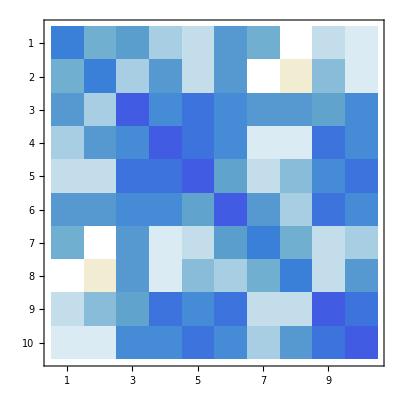

```mathematica
MatrixPlot[LL]
```

```mathematica
xvec = LinearSolve[LL,vv]
```

{-0.109303,-0.118326,-0.622478,-0.511662,0.214112,-0.622478,-0.109303,-0.118326,0.214112,-0.511662}

```mathematica
chi[q_]:=Sum[
xvec[[i]] * Fo[q,octree[[i]][[1]][[1]],octree[[i]][[1]][[2]]]
,{i,nleaves}]
```

```mathematica
γ = Mean[Table[chi[sp[[i]]],{i,npoints}]];
```

```mathematica
cp = ContourPlot3D[chi[{x,y,z}]==γ,{x,xmin,xmax},{y,ymin,ymax},{z,zmin,zmax},Mesh-> None,  ContourStyle-> {Green, Opacity[0.2]}];
```

```mathematica
Show[
cp,
ListPointPlot3D[sp, BoxRatios->1]
]
```

-Graphics3D-